## Model Setup

```mathematica
wm = ResourceFunction["WolframModel"];
plot = ResourceFunction["WolframModelPlot"];
randomRule = ResourceFunction["RandomWolframModel"];
```

```mathematica
steps=10;
maxValue = 3;
maxVertices=3;
```

```mathematica
randomSignature[maxRelations_, maxElements_, maxPieces_] := 
	Rule @@ Table[
		Table[
			{RandomInteger[{1, maxRelations}], RandomInteger[{1, maxElements}]},
			RandomInteger[{1, maxPieces}]
		], 
		2
	]
```

```mathematica
signature = randomSignature[3, 3, 2]
```

{{3,1},{1,1}}→{{1,3}}

```mathematica
signature={{2,2}}->{{4,2}}
```

{{2,2}}→{{4,2}}

```mathematica
rule=randomRule[signature]
```

{{1,2},{2,3}}→{{4,5},{4,1},{5,3},{2,1}}

```mathematica
init = Array[Function[1],signature[[1]][[1]]]
```

{{1,1},{1,1}}

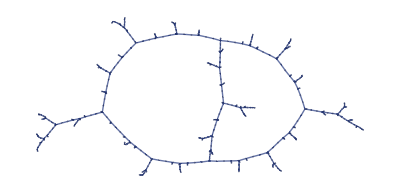

```mathematica
wm[rule, init, steps, "FinalStatePlot"]
```

## Mutations

```mathematica
rule = {rule}
```

{{{1,2},{2,3}}→{{4,5},{4,1},{5,3},{2,1}}}

```mathematica
selectElement[rule_]:=
Module[{replacement, side, edge, vertex, x},
replacement=RandomInteger[{1, Length[rule]}];
x = rule[[replacement]];
side = RandomInteger[{1, 2}];
x = x[[side]];
edge = RandomInteger[{1, Length[x]}];
x = x[[edge]];
vertex = RandomInteger[{1, Length[x]}];
{replacement, side, edge, vertex}
]
```

```mathematica
maxElement[rule_]:=Max[Flatten[List@@@rule]]
```

```mathematica
replaceRandomElement[rule_]:=
ReplacePart[rule, selectElement[rule]->RandomInteger[{1,maxElement[rule]}]]
```

```mathematica
rule
```

{{{1,2},{2,3}}→{{4,5},{4,1},{5,3},{2,1}}}

```mathematica
newRule=replaceRandomElement[rule]
```

{{{1,2},{2,3}}→{{4,3},{4,1},{5,3},{2,1}}}

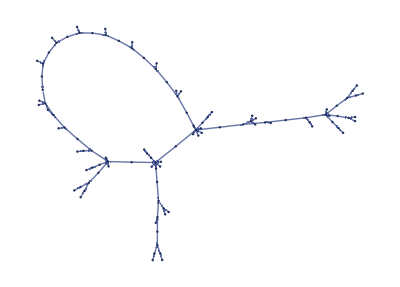

```mathematica
wm[newRule, init, steps, "FinalStatePlot"]
```